## Wood-Saxon

```mathematica
RA[A_]:=119/100 A^(1/3)-161/100 A^(-1/3)
d=54/100;
n0[A_]:=3/4 A/(π RA[A]^3)1/(1+((π d)/RA[A])^2)
ρ0=17/100;
```

```mathematica
integrand[s_,z_,A_]:=n0[A]/(1+Exp[(√(s^2+z^2)-RA[A])/d])
```

```mathematica
ρ[r_,A_]:=ρ0/(1+Exp[(r-RA[A])/d])
ρ[s_,z_,A_]:=ρ[√(s^2+z^2),A]
```

```mathematica
TA[s_,A_]:=NIntegrate[integrand[s,z,A],{z,-∞,∞}]
```

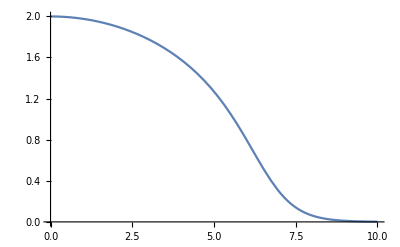

```mathematica
Plot[TA[s,197],{s,0,10}]
```

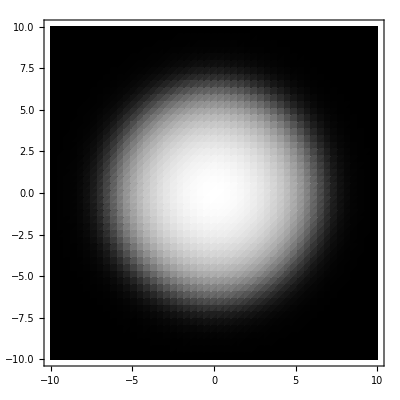

```mathematica
DensityPlot[TA[Norm[{sx,sy}],197],{sx,-10,10},{sy,-10,10},PlotPoints->50,ColorFunction->GrayLevel]
```

```mathematica
total[A_]=Integrate[integrand[Norm[{sx,sy}],z,A],{z,-∞,∞},{sx,-∞,∞},{sy,-∞,∞}]
```

-(944784 A^2 PolyLog[3,-ⅇ^(-5/(6 A^(1/3))+(59 A^(1/3))/27)])/((-45+118 A^(2/3)) (2025-10620 A^(2/3)+13924 A^(4/3)+2916 A^(2/3) π^2))

```mathematica
total[1]//N
total[197]//N
```

1.09523

197.

```mathematica
NIntegrate[(ρ[Norm[{sx,sy}],z,27])^2,{z,-∞,∞},{sx,-∞,∞},{sy,-∞,∞}]
```

2.44374

```mathematica
NIntegrate[(ρ[Norm[{sx,sy}],z,197])^2,{z,-∞,∞},{sx,-∞,∞},{sy,-∞,∞}]
```

29.0217